```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\hfukuda\git\phys_slides\susy2018

```mathematica
xs = Interpolation[ReadList["./xs.dat",{Number,Number}]/.{m_,xs_}->{m,Log[xs]}]
```

InterpolatingFunction[{{100., 2000.}}, <>]

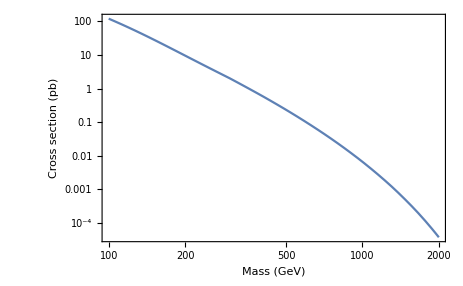

```mathematica
fig = LogLogPlot[Exp[xs[mass]], {mass, 100, 2000},Frame->True,FrameLabel->{Style["Mass (GeV)", 16],Style["Cross section (pb)", 16]}]
```

```mathematica
Export["xs.pdf", fig]
```

xs.pdf

```mathematica
xs[100]
```

4.79165